```mathematica
DSolve[{y'[x]==Sin[5*x]},y[x],x]
```

{{y[x]→C[1]-1/5 Cos[5 x]}}

```mathematica
DSolve[{x^2*y'[x]==y[x]-y[x]*x},y[x],x]
```

{{y[x]→(ⅇ^(-1/x) C[1])/x}}

```mathematica
DSolve[{x^2*y'[x]==y[x]-y[x]*x,y[1]==1/ⅇ},y[x],x]
```

{{y[x]→ⅇ^(-1/x)/x}}

```mathematica
DSolve[{y''[x]+5y'[x]+2y[x]==0,y[0]==5,y'[0]==10},y[x],x]
```

{{y[x]→-5/34 (-17 ⅇ^((-5/2-(√17)/2) x)+9 √17 ⅇ^((-5/2-(√17)/2) x)-17 ⅇ^((-5/2+(√17)/2) x)-9 √17 ⅇ^((-5/2+(√17)/2) x))}}

```mathematica
DSolve[{y''[x]+5y'[x]+2y[x]==0},y[x],x]
```

{{y[x]→ⅇ^((-5/2-(√17)/2) x) C[1]+ⅇ^((-5/2+(√17)/2) x) C[2]}}

```mathematica
a=NDSolve[{y''[x]+x*y[x]==0,y[0]==1,y[1]==1},y[x],{x,-5,10}]
```

{{y[x]→InterpolatingFunction[{{-5.,10.}},<>][x]}}

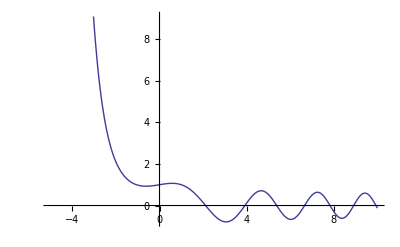

NDSolve::deqn: Equation or list of equations expected instead of 1 in the first argument {y[t] + SuperscriptBox["y", "′",MultilineFunction->None][t]\\ SuperscriptBox[RowBox[{"(", RowBox[{"1", "+", RowBox[{SuperscriptBox["y", "′",MultilineFunction->None], "[", "t", "]"}]}], ")"}], "2"] + SuperscriptBox["y", "′′",MultilineFunction->None][t] == 0, 1, SuperscriptBox["y", "′",MultilineFunction->None][0] == 0}. ButtonBox["»",Appearance->{Automatic, None, "Normal", Automatic},BaseStyle->"Link",ButtonData:>"paclet:ref/message/NDSolve/deqn",ButtonNote->"NDSolve::deqn"]

NDSolve::deqn: Equation or list of equations expected instead of 1 in the first argument y[t] + SuperscriptBox[1SuperscriptBox[.

NDSolve::deqn: Equation or list of equations expected instead of 1 in the first argument {y[t] + SuperscriptBox["y", "′",MultilineFunction->None][t]\\ SuperscriptBox[RowBox[{"(", RowBox[{"1", "+", RowBox[{SuperscriptBox["y", "′",MultilineFunction->None], "[", "t", "]"}]}], ")"}], "2"] + SuperscriptBox["y", "′′",MultilineFunction->None][t] == 0, 1, SuperscriptBox["y", "′",MultilineFunction->None][0] == 0}. ButtonBox["»",Appearance->{Automatic, None, "Normal", Automatic},BaseStyle->"Link",ButtonData:>"paclet:ref/message/NDSolve/deqn",ButtonNote->"NDSolve::deqn"]

NDSolve::deqn: Equation or list of equations expected instead of 1 in the first argument y[t] + SuperscriptBox[1SuperscriptBox[.

NDSolve::deqn: Equation or list of equations expected instead of 1 in the first argument {y[t] + SuperscriptBox[\"y\", \"′\",MultilineFunction->None][t]\\\ SuperscriptBox[RowBox[{\"(\", RowBox[{\"1\", \"+\", RowBox[{SuperscriptBox[\"y\", \"′\",MultilineFunction->None], \"[\", \"t\", \"]\"}]}], \")\"}], \"2\"] + SuperscriptBox[\"y\", \"′′\",MultilineFunction->None][t] == 0, 1, SuperscriptBox[\"y\", \"′\",MultilineFunction->None][0] == 0}.

```mathematica
Plot[Evaluate[y[x]/.a],{x,-5,10}]
```

{{y[t]→InterpolatingFunction[…][t]}}

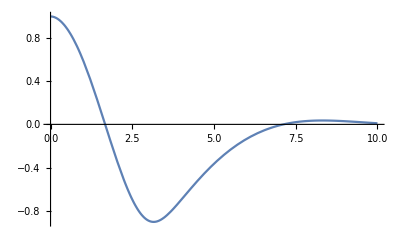

```mathematica
b=NDSolve[{y''[t]+(y'[t]+1)^2*y'[t]+y[t]==0,y[0]==1,y'[0]==0},y[t],{t,0,10}]

Plot[Evaluate[y[t]/.b],{t,0,10}]
```

```mathematica
DSolve[{L*Q''[t]+R*Q'[t]+1/C*Q[t]==Subscript[V, 0]*ⅇ^(j*ω*t)},Q[t],t]
```

{{Q[t]→ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t) C[1]+ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t) C[2]-(2 C L (√C ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R-√C ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) R+ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) √(-4 L+C R^2)+2 √C ⅇ^(1/2 (-R/L+(√(-4 L+C R^2))/(√C L)) t+(t (R-(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω-2 √C ⅇ^(1/2 (-R/L-(√(-4 L+C R^2))/(√C L)) t+(t (R+(√(-4 L+C R^2))/(√C)+2 j L ω))/(2 L)) j L ω) V_0)/(√(-4 L+C R^2) (-√C R+√(-4 L+C R^2)-2 √C j L ω) (√C R+√(-4 L+C R^2)+2 √C j L ω))}}